# Integer Partitions: A Brief Overview And A Combinatorics Application

Albert Tang, June 28 2019

Integer partition is a way of writing out a positive integer n as a sum of positive integers. For example, there are 8 ways to partition n = 5, as shown below:

```mathematica
Column[IntegerPartitions[5]]
```

{5}
{4,1}
{3,2}
{3,1,1}
{2,2,1}
{2,1,1,1}
{1,1,1,1,1}

One may also examine the number of ways to partition n into m parts for some integer m <= n. Note that since each of the parts are greater or equal to 1 the value m has to be no greater than n.

```mathematica
Column[IntegerPartitions[5,{3}]]
```

{3,1,1}
{2,2,1}

One common question regarding integer partitions is to examine how many ways can one partition a given number n, or examining how many ways can one partition a given number n into m parts. For example, there is a total of 42 ways to partition n = 10:

```mathematica
numberPartitions[n_Integer] := Length[IntegerPartitions[n]]
```

```mathematica
numberPartitions[10]
```

42

We may also break down how many ways we may break down the 42 partitions and see how many ways can one partition 10 into m parts, for 1 <= m <= 10:

```mathematica
Range[10] -> Table[Length[IntegerPartitions[10,{m}]],{m,10}]
```

{1,2,3,4,5,6,7,8,9,10}→{1,5,8,9,7,5,3,2,1,1}

One may wonder at this point how one may determine the number of partitions of n without listing every single partition example, which is extremely cumbersome if n is of a large value.

There is a property that will allow us to examine this question. Let us suppose we are partitioning 10 into m parts. Then each of the parts have to be greater than or equal to 1. This means that there is only (10-m) left to distribute to n parts after each of the m parts have been given 1. This means that the number of ways to partition 10 into m parts must be equal to the number of ways to partition (10-m) into a parts for all m less than equal to a.

We can express this property using Ferrer’s Diagram. Ferrer’s Diagram is very commonly used to express an integer partition in diagram form where each part k in the partition is expressed as k dots horizontally, each part in a different row. The example below shows how one may express the partition {4,4,1,1} of the number 10:

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

FerrersDiagram::shdw: Symbol FerrersDiagram appears in multiple contexts {Combinatorica`,Global`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

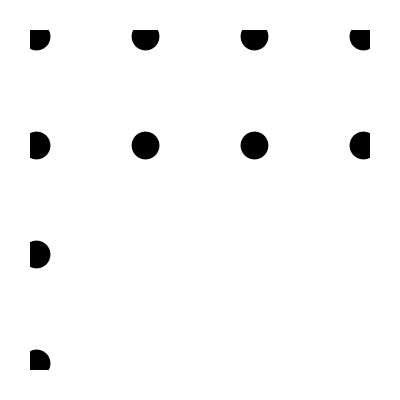

```mathematica
FerrersDiagram[{4,4,1,1}]
```

With Ferrer’s digram, we can illustrate why my claim is true by splitting the dots into two categories. The category of the dots colored in red is the first dot for every number, and there will be a total of m dots. Then, the (10-m) dots that are left will be distributed in forms of the blue dots. The blue dots may be distributed into 1, 2, 3, or 4 groups. The diagram below displays how the coloring may be done for {4,4,1,1}. As we can see, the blue dots will form the partition {3,3}.

```mathematica
FullForm[FerrersDiagram[{4,4,1,1}]]
```

Graphics[List[PointSize[0.05],List[Point[List[1,1]]],List[Point[List[1,2]]],List[Point[List[1,3]],Point[List[2,3]],Point[List[3,3]],Point[List[4,3]]],List[Point[List[1,4]],Point[List[2,4]],Point[List[3,4]],Point[List[4,4]]]],List[Rule[AspectRatio,1],Rule[PlotRange,All]]]

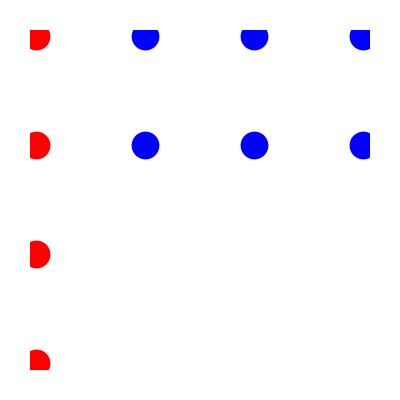

```mathematica
Graphics[List[PointSize[0.05],List[Style[Point[List[1,1]],Red]],List[Style[Point[List[1,2]],Red]],List[Style[Point[List[1,3]],Red],Style[Point[List[2,3]],Blue],Style[Point[List[3,3]],Blue],Style[Point[List[4,3]],Blue]],List[Style[Point[List[1,4]],Red],Style[Point[List[2,4]],Blue],Style[Point[List[3,4]],Blue],Style[Point[List[4,4]],Blue]]],List[Rule[AspectRatio,1],Rule[PlotRange,All]]]
```

Using this property that is demonstrated by the diagram above, finding a number of partitions of n into m parts is equivalent to partitioning (n-m) into at most m or (n-m) parts, which ever number is slower. Using this property, we can find the number of ways to partition 10 into m parts where m is 1,2,3,...,10, and then proceed to verify that the number of partitions of 10 is indeed 42.

```mathematica
addSubNumberPartitions[n_Integer] := ReplacePart[Table[Total[Length[IntegerPartitions[n-m,{#}]]&/@Range[m]],{m,n}],{n -> 1}]
```

```mathematica
addSubNumberPartitions[10]
```

{1,5,8,9,7,5,3,2,1,1}

```mathematica
Total[addSubNumberPartitions[10]]
```

42

Now the question arises on whether the subject of integer partitions may be used in other areas. After given some thought, I found a way to apply knowledge regarding integer partitions. Let us there is a pile of n discrete objects and you have exactly k of them. Your friend tells you that he has at least one object but you do not know how many of them your friend has. You also do not know how many people is this object distributed to. The question is: Can you determine the probability that your friend has less, more, or an equal number of objects compared to you?

This is where integer partitions could come in handy. Given that the n values are determined, and also the fact that k must exist in the partition, we know exactly what partitions are possible. In each of these partitions, the quantity of objects that your friend may have, as well as the number of possible ways to achieve that quantity, is set.

```mathematica
possiblePartitions[n_Integer,m_Integer] := Select[IntegerPartitions[n],MemberQ[#,m]&]
```

```mathematica
possiblePartitions[8,3]
```

{{5,3},{4,3,1},{3,3,2},{3,3,1,1},{3,2,2,1},{3,2,1,1,1},{3,1,1,1,1,1}}

With these partitions, we can determine, discluding itself, what the probability of having a part less than, equal to, and greater than the quantity that you have. First, we take out the m objects that you have.

```mathematica
useablePartitions[n_Integer,m_Integer] :=Delete[#,Min[Position[#,m]]]&/@possiblePartitions[n,m]
```

```mathematica
useablePartitions[8,3]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

Using these partitions, we can use the distributed function to determine, for each of these cases, what the probability is for the friend to get less than, equal to, or more than m. Then we average out the probabilities in each of these distributions to determine the overall probability.

```mathematica
probLower[n_Integer,m_Integer]/;n>m := Mean[Probability[x < m,Distributed[x,#]]&/@useablePartitions[n,m]]
```

```mathematica
probHigher[n_Integer,m_Integer]/;n>m := Mean[Probability[x>m,Distributed[x,#]]&/@useablePartitions[n,m]]
```

```mathematica
probEqual[n_Integer,m_Integer]/;n>m := 1 - probLower[n,m] - probHigher[n,m]
```

```mathematica
probLoEqHi[n_Integer,m_Integer]/;n>m := {probLower[n,m],probEqual[n,m],probHigher[n,m]}
```

```mathematica
probLoEqHi[8,3]
```

{2/3,5/42,3/14}

So we can use this to conclude that if there are a total of 8 objects, and you have 3, the probability of your friend having less than, equal to, or more than the number of objects that you have is 2/3, 5/42, and 3/14, respectively.

We can even generate a simulation where the user can input the total number of objects and the number of objects they have to see the probabilities:

```mathematica
Manipulate[PieChart[Table[Labeled[Part[probLoEqHi[n,m],i],N[Part[probLoEqHi[n,m],i],4]],{i,3}],ChartLegends -> {"Lower","Equal","Higher"}],{n,2,50,1},{m,1,n-1,1}]
```

We can take this even further and ask another question: Given the total number of objects n, how does m change the probabilities? Well, we create a line graph simulation to demonstrate that. We will start with n=4 since n=2 and n=3 is almost trivial: if n=2 then the partition is {1,1}, and If n = 3 then the partitions are {2,1}, or {1,1,1} (there has to be at least two numbers in the partition). Using that, the probability can be easy reduced.

```mathematica
graphLoEqHi[n_Integer] := ListLinePlot[Transpose[probLoEqHi[n,#]&/@ Range[n-1]], PlotLegends->{"Lower","Equal","Higher"}]
```

```mathematica
Manipulate[graphLoEqHi[n],{n,4,20,1}]
```

From the graph we can notice two things. One, for m value that are greater than n/2 the probability of the friend having a lower value is 1. Mathematically this makes sense considering that otherwise there exists a case where you can your friend both have more than n/2 objects, which brings the total to greater than n, which cannot be true. Second of all, we notice that there realistically only exist a few m values where the probability of your friend having a lower quantity of objects is lower than the other two probability. This likely means that the occurrence of small parts such as 1 or 2 is extremely common among integer partitions.

Considering that this equates to the matter of people being given of number m out of a list of n objects, another method that one can think of it using binomial to determine the probability of the friends having less than, more than, or equal to the number. How does this work? After the first person, which is you, takes m objects, there is a total of (n-m) objects left. These (n-m) objects, which are all equal, will be distributed among at most (n-m) people.
We can graphically visualize this scenario: We can line up the (n-m) objects in a row and place a total of (n-m-1) sticks between the (n-m) objects. Note that there may be multiple sticks between two consecutive objects. We know that there will then be a total P(2n-2m-1, n-m-1) ways to do so. Let us suppose that your friend will always get the objects to the left of the first stick. Suppose the friend has gotten k objects. This means that the identity of the first (k+1) things  is confirmed (k objects and 1 stick). To the right of the first stick, there will be a total of (2n-2m-1-(k+1)) objects to be arranged, a total of (n-m-2) of them being sticks. Thus, there will be a total of P(2n-2m-1-(k+1), n-m-2) ways to arrange these objects and stick. Thus, if one knows what the value of 2n-2m-1-(k+1) is, we can figure out whether x is less than, more than, or equal to m. As a result, we can use the binomial function to create a function, probCalcBinominal[n,m], that determines the probability of which your friend has more than, less than, or equal to the number of objects that you own.

```mathematica
probLowerBino[n_Integer,m_Integer] := Total[Table[Binomial[x,n-m-2],{x,2(n-m)-2 -(m-1),2(n-m)-2}]]/Binomial[2(n-m)-1,n-m-1]
```

```mathematica
probSameBino[n_Integer,m_Integer] := Total[Binomial[2(n-m) - 2 - (m-1) - 1, n-m-2]]/Binomial[2(n-m)-1,n-m-1]
```

```mathematica
probHighBino[n_Integer,m_Integer] := 1 - probLowerBino[n,m]-probSameBino[n,m]
```

```mathematica
probCalcBinomial[n_Integer,m_Integer] := {probLowerBino[n,m],probSameBino[n,m],probHighBino[n,m]}
```

Notice in this case, the probabilities calculated using binomial will be different from the probabilities calculated using integer partitions:

```mathematica
N[probCalcBinomial[8,3],4]
```

{0.881,0.07937,0.03968}

```mathematica
N[probLoEqHi[8,3],4]
```

{0.6667,0.119,0.2143}

Notice that the probability that the friend has higher quantity than you is significantly higher. Why? Because in the integer partition scenario we assumed that each case is equally likely to happen. For instance, the partition {5,3} is assumed to be equally likely as {3,1,1,1,1,1}, where as when we are approximating using binomial the probability of the latter happening is much higher. Using combinatorics, we know that the number of chances of {5,3} happening is (8!)/[(5!){3!)] = 56, where as the number of chances of {3,1,1,1,1,1} happening is (8!)/[(3!)(1!)(1!)(1!)(1!)(1!)] = 6720. Thus, the chances of each partition occurring is not the same, and we have to apply a weighted average based on how likely each scenario is to occur obtain an accurate result. This will be an interesting topic to study in the future. With that being said, it remains true that integer partitions is an interesting topic with useful applications.